```mathematica
Play[Sin[220 2Pi t*1],{t,0,3/2}]
```

-Graphics-

```mathematica
Play[Sin[220 2Pi t*1.5],{t,0,3/2}]
```

-Graphics-

```mathematica
Play[Sin[220 2Pi t*((24/25)/(5/8))],{t,0,3/2},SampleRate->64000]
```

-Graphics-

```mathematica
Play[Sin[220 2Pi t*(3/2)]+Sin[220 2Pi t],{t,0,3/2},SampleRate->64000]
```

-Graphics-

```mathematica
Play[Sin[220 2Pi t*((24/25)/(5/8))]+Sin[220 2Pi t],{t,0,3/2},SampleRate->64000]
```

-Graphics-

```mathematica
Play[Sin[220 2Pi t*(8/5)]+Sin[220 2Pi t],{t,0,3/2},SampleRate->64000]
```

-Graphics-

```mathematica
Manipulate[Play[Sin[1000t]+Sin[(1000+x)t],{t,0,2}],{x,0,20}]
```

We need to add the waveforms together. "Superposition" principle. See page 619 of the physics book that Louis gave you.

Unison

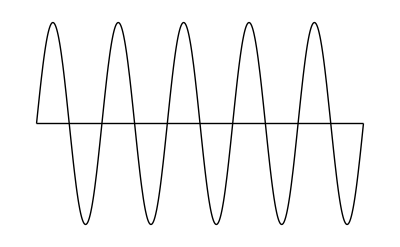

```mathematica
basic = Plot[{Sin[x],0},{x,0,5*2Pi},Ticks->False,Axes ->False,PlotStyle->Black]
```

```mathematica
Export["basicWave.pdf",basic]
```

basicWave.pdf

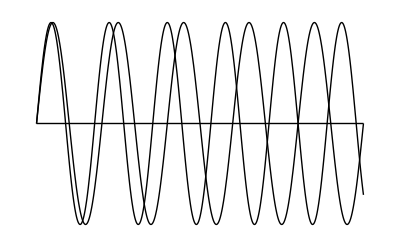

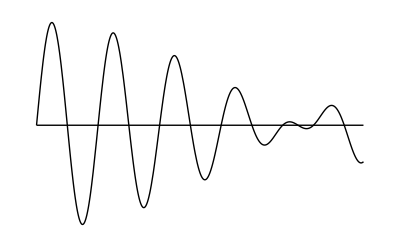

```mathematica
superComb =Plot[{Sin[x],Sin[x*9/8],0},{x,0,5*2Pi},Ticks->False,Axes->False,PlotStyle->{Black}]
superSum =Plot[{Sin[x]+Sin[x*9/8],0},{x,0,5*2Pi},Ticks->False,Axes->False,PlotRange->All,PlotStyle->{Black}]
```

```mathematica
Export["superSum.pdf",superSum]
Export["superComb.pdf",superComb]
```

superSum.pdf

superComb.pdf

Major Second

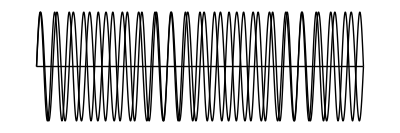

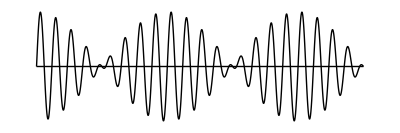

```mathematica
minorComb =Plot[{Sin[x],Sin[x*9/8],0},{x,0,20*2Pi},Ticks->False,Axes->False,PlotStyle->{Black},AspectRatio->1/3]
minorSum =Plot[{Sin[x]+Sin[x*9/8],0},{x,0,20*2Pi},Ticks->False,Axes->False,PlotStyle->{Black},AspectRatio->1/3]
```

```mathematica
Export["minorSum.pdf",minorSum]
Export["minorComb.pdf",minorComb]
```

minorSum.pdf

minorComb.pdf

perfect 5th

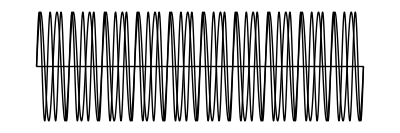

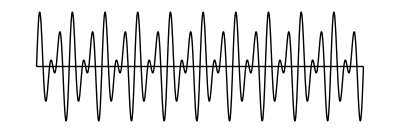

```mathematica
fifthComb=Plot[{Sin[x],Sin[x*3/2],0},{x,0,20*2Pi},Axes->False,Ticks->False,PlotStyle->Black,AspectRatio->1/3]
fifthSum=Plot[{Sin[x]+Sin[x*3/2],0},{x,0,20*2Pi},Axes->False,Ticks->False,PlotStyle->Black,PlotRange->All,AspectRatio->1/3]
```

```mathematica
Export["fifthSum.pdf",fifthSum]
Export["fifthComb.pdf",fifthComb]
```

fifthSum.pdf

fifthComb.pdf

octave

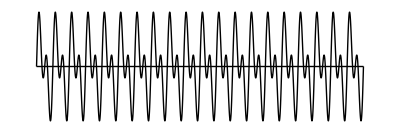

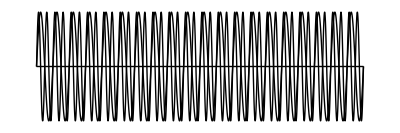

```mathematica
octaveSum = Plot[{Sin[x]+Sin[x*2],0},{x,0,20*2Pi},Axes->False,Ticks->False,PlotStyle->Black,AspectRatio->1/3]
octaveComb = Plot[{Sin[x],Sin[x*2],0},{x,0,20*2Pi},Axes->False,Ticks->False,PlotStyle->Black,AspectRatio->1/3]
```

```mathematica
Export["octaveSum.pdf",octaveSum]
Export["octaveComb.pdf",octaveComb]
```

octaveSum.pdf

octaveComb.pdf

### Basic Examples (1)

Play a "middle A" sine wave for 1 second:

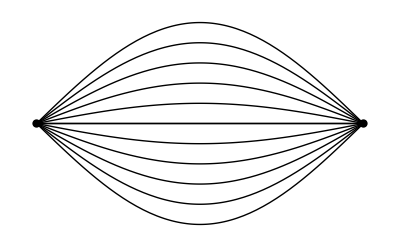

```mathematica
line=Plot[{0},{x,0,2Pi},Axes->False,Ticks->False,PlotStyle->Black];
pcurve=Plot[Table[i*Sin[x /2],{i,-1,1,.2}],{x,0,2Pi},Axes->False,Ticks->False,PlotStyle->{Black}];
stand=Show[line,pcurve,Graphics[{PointSize[.015],Point[{{0,0},{2Pi,0}}]}]]
```

```mathematica
Export["stand.pdf",stand]
```

stand.pdf

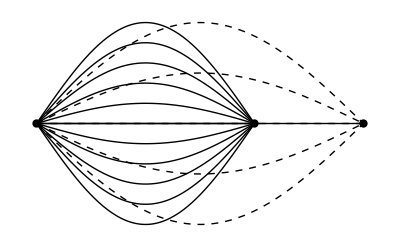

```mathematica
line=Plot[{0},{x,0,2Pi},Axes->False,Ticks->False,PlotStyle->Black];
pcurve=Plot[Table[i*Sin[x /2],{i,-1,1,.5}],{x,0,2Pi},Axes->False,Ticks->False,PlotStyle->{Dashed,Black}];
curve=Plot[Table[i*Sin[x 3/4],{i,-1,1,.2}],{x,0,4Pi/3},Axes->False,Ticks->False,PlotStyle->Black];
dom1=Show[line,curve,pcurve,Graphics[{PointSize[.015],Point[{{0,0},{4Pi/3,0},{2Pi,0}}]}]]
```

```mathematica
Export["dom1.pdf",dom1]
```

dom1.pdf

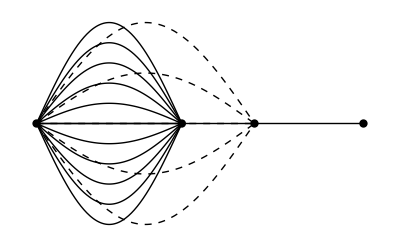

```mathematica
line=Plot[{0},{x,0,2Pi},Axes->False,Ticks->False,PlotStyle->Black];
bcurve=Plot[Table[i Sin[x 3/4],{i,-1,1,.5}],{x,0,4Pi/3},Axes->False,Ticks->False,PlotStyle->{Dashed,Black}];
curve=Plot[Table[i Sin[x 3^2/2^3],{i,-1,1,.2}],{x,0,8Pi/9},Axes->False,Ticks->False,PlotStyle->Black];
pdom2=Show[line,bcurve,curve,Graphics[{PointSize[.015],Point[{{0,0},{4Pi/3,0},{8Pi/9,0},{2Pi,0}}]}]]
```

```mathematica
Export["pdom2.pdf",pdom2]
```

pdom2.pdf

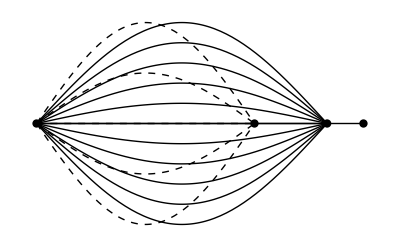

```mathematica
line=Plot[{0},{x,0,2Pi},Axes->False,Ticks->False,PlotStyle->Black];
bcurve=Plot[Table[i Sin[x 3/4],{i,-1,1,.5}],{x,0,4Pi/3},Axes->False,Ticks->False,PlotStyle->{Dashed,Black}];
curve=Plot[Table[i Sin[x 3^2/2^4],{i,-1,1,.2}],{x,0,16Pi/9},Axes->False,Ticks->False,PlotStyle->Black];
dom2=Show[line,bcurve,curve,Graphics[{PointSize[.015],Point[{{0,0},{4Pi/3,0},{16Pi/9,0},{2Pi,0}}]}]]
```

```mathematica
Export["dom2.pdf",dom2]
```

dom2.pdf

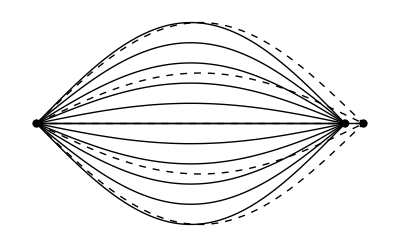

```mathematica
line=Plot[{0},{x,0,2Pi},Axes->False,Ticks->False,PlotStyle->Black];
bcurve=Plot[Table[i Sin[x /2],{i,-1,1,.5}],{x,0,2Pi},Axes->False,Ticks->False,PlotStyle->{Dashed,Black}];
curve=Plot[Table[i Sin[x 2^(1/12)/2],{i,-1,1,.2}],{x,0,2Pi/(2^(1/12))},Axes->False,Ticks->False,PlotStyle->Black];
firstFret=Show[line,bcurve,curve,Graphics[{PointSize[.015],Point[{{0,0},{2Pi/(2^(1/12)),0},{2Pi,0}}]}]]
```

```mathematica
Export["firstFret.pdf",firstFret]
```

firstFret.pdf

Now we will try to derive the 12 tones......

If[(2 t)/3<0.49,(4 t)/3,(2 t)/3]

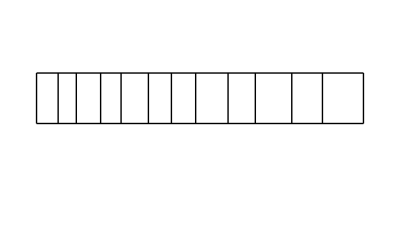

```mathematica
fret[t_]=If[(2/3)t<1/2-.01, (4/3) t,(2/3 )t]
line=Plot[{0},{x,.49327,1},Axes->False,PlotStyle->{Black,Thick}];
line2=Plot[{.5},{x,.49327,1},PlotStyle->{Black,Thick}];
Frets=Line[Table[{{(NestList[fret,1,12])[[i]],0},{(NestList[fret,1,12])[[i]],.5}},{i,1,13}]];
fboard1 = Show[line,line2,Graphics[{PointSize[.015],Black,Frets}]]
```

```mathematica
Export["fboard1.svg",fboard1]
```

fboard1.svg

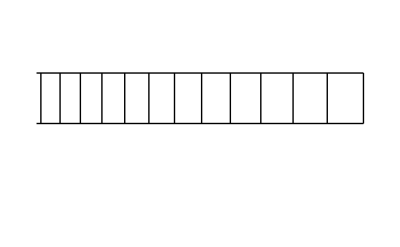

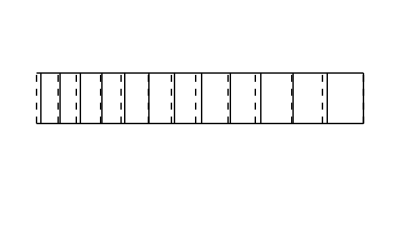

```mathematica
line=Plot[{0},{x,.49327,1},Axes->False,Ticks->False,PlotStyle->{Black,Thick}];
line2=Plot[{.5},{x,.49327,1},Axes->False,Ticks->False,PlotStyle->{Black,Thick}];
Frets=Line[Table[{{(NestList[fret,1,12])[[i]],0},{NestList[fret,1,12][[i]],.5}},{i,1,13}]];FretsApprox=Line[Table[{{(Flatten[Table[1/2^{i/12},{i,0,12}]])[[i]],0},{(Flatten[Table[1/2^{i/12},{i,0,12}]])[[i]],.5}},{i,1,13}]];
equalfret=Show[line,line2,Graphics[{Black,FretsApprox}]]
bfret=Show[line,line2,Graphics[{Dashed,Frets}],Graphics[{Black,FretsApprox}]]
```

```mathematica
Export["eqFret.svg",equalfret]
Export["bFret.svg",bfret]
```

eqFret.svg

bFret.svg

```mathematica
ContinuedFractionForm[ContinuedFraction[Log[3,2],6]]
```

0+1/(1+1/(1+1/(1+1/(2+1/2))))

```mathematica
fretE[t_]=If[Log[3,2]t<1/2-.01, (Log[3.,2])2 t,(Log[3.,2] )t]
```

If[(t Log[2])/Log[3]<0.49,Log[3.,2] 2 t,Log[3.,2] t]

```mathematica
NestList[fretE,1,12]
```

{1,0.63093,0.796145,0.502311,0.633846,0.799825,0.504633,0.636777,0.803523,0.506966,0.63972,0.807237,0.50931}

Point[{{2 π,0},{3.96425,0},{5.00232,0},{3.15612,0},{3.98257,0},{5.02545,0},{3.17071,0},{4.00098,0},{5.04868,0},{3.18536,0},{4.01948,0},{5.07202,0},{3.20009,0}}]

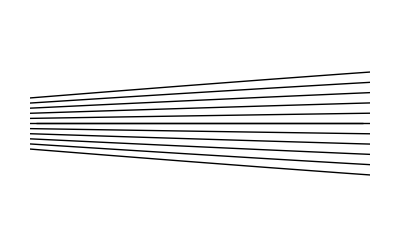

```mathematica
Frets=Point[Table[{(2Pi*NestList[fretE,1,12])[[i]],0},{i,1,13}]]
Show[line,curve,Graphics[{PointSize[.015],Frets}]]
```

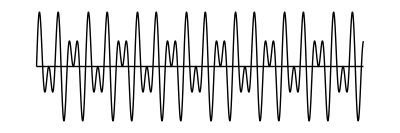

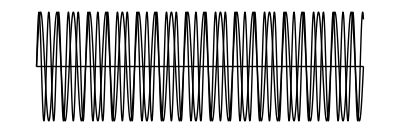

```mathematica
p1Sum = Plot[{Sin[x]+Sin[x*5/3],0},{x,0,20*2Pi},Axes->False,Ticks->False,PlotRange->All,PlotStyle->Black,AspectRatio->1/3]
p1Comb = Plot[{Sin[x],Sin[x*5/3],0},{x,0,20*2Pi},Axes->False,Ticks->False,PlotStyle->Black,AspectRatio->1/3]
```

```mathematica
Export["p1Sum.pdf",p1Sum]
Export["p1Comb.pdf",p1Comb]
```

p1Sum.pdf

p1Comb.pdf

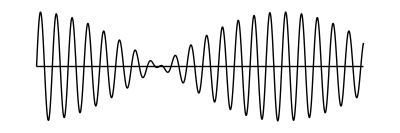

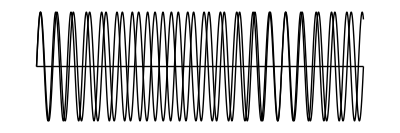

```mathematica
p2Sum = Plot[{Sin[x]+Sin[x*16/15],0},{x,0,20*2Pi},Axes->False,Ticks->False,PlotRange->All,PlotStyle->Black,AspectRatio->1/3]
p2Comb = Plot[{Sin[x],Sin[x*16/15],0},{x,0,20*2Pi},Axes->False,Ticks->False,PlotStyle->Black,AspectRatio->1/3]
```

```mathematica
Export["p2Sum.pdf",p2Sum]
Export["p2Comb.pdf",p2Comb]
```

p2Sum.pdf

p2Comb.pdf

Now let's start with 3/4

```mathematica
fret[t_]=If[(3/4.)t<1/2, (6/4.) t,(3./4 )t]
NestList[fret,1,12]
```

If[0.75 t<1/2,(6 t)/4.,(3. t)/4]

{1,0.75,0.5625,0.84375,0.632813,0.949219,0.711914,0.533936,0.800903,0.600677,0.901016,0.675762,0.506822}

```mathematica
FromContinuedFraction[ContinuedFraction[Log[3,4],4]]
```

24/19

```mathematica
3.^(4/5)
```

2.40822

```mathematica
2^(1/12.)
```

1.05946

Now let's start with 4/5

```mathematica
fret[t_]=If[(4/5.)t<1/2, (8/5.) t,(4./5 )t]
NestList[fret,1,29]
```

If[0.8 t<1/2,(8 t)/5.,(4. t)/5]

{1,0.8,0.64,0.512,0.8192,0.65536,0.524288,0.838861,0.671089,0.536871,0.858993,0.687195,0.549756,0.879609,0.703687,0.56295,0.90072,0.720576,0.576461,0.922337,0.73787,0.590296,0.944473,0.755579,0.604463,0.967141,0.773713,0.61897,0.990352,0.792282}

```mathematica
FromContinuedFraction[ContinuedFraction[Log[4,5],2]]
```

7/6

```mathematica
FromContinuedFraction[ContinuedFraction[Log[2,3],4]]
```

8/5

```mathematica
fret[t_]=If[(2/3.)t<1/2-.01, (4/3.) t,(2./3 )t]
NestList[fret,1,29]
```

If[0.666667 t<0.49,(4 t)/3.,(2. t)/3]

{1,0.666667,0.888889,0.592593,0.790123,0.526749,0.702332,0.936443,0.624295,0.832393,0.554929,0.739905,0.49327,0.657694,0.876925,0.584617,0.779489,0.519659,0.692879,0.923838,0.615892,0.82119,0.54746,0.729946,0.973262,0.648841,0.865122,0.576748,0.768997,0.512665}